```mathematica
A={{1,0,0},{Subscript[ρ, 2,1],Sqrt[1-Subscript[ρ, 2,1]^2],0},{Subscript[ρ, 3,1],x,y}}
```

{{1,0,0},{ρ_(2,1),√(1-ρ_(2,1)^2),0},{ρ_(3,1),x,y}}

```mathematica
A .Transpose[A]=={{1,Subscript[ρ, 2,1],Subscript[ρ, 3,1]},{Subscript[ρ, 2,1],1,Subscript[ρ, 3,2]},{Subscript[ρ, 3,1],Subscript[ρ, 3,2],1}}//TraditionalForm
```

(1 | ρ_(2,1) | ρ_(3,1)
ρ_(2,1) | 1 | √(1-ρ_(2,1)^2) x+ρ_(2,1) ρ_(3,1)
ρ_(3,1) | √(1-ρ_(2,1)^2) x+ρ_(2,1) ρ_(3,1) | x^2+y^2+ρ_(3,1)^2)==(1 | ρ_(2,1) | ρ_(3,1)
ρ_(2,1) | 1 | ρ_(3,2)
ρ_(3,1) | ρ_(3,2) | 1)

```mathematica
Solve[{√(1-Subscript[ρ, 2,1]^2) x+Subscript[ρ, 2,1] Subscript[ρ, 3,1]==Subscript[ρ, 3,2],x^2+y^2+Subscript[ρ, 3,1]^2==1},{x,y}]//Simplify
```

{{x→(-ρ_(2,1) ρ_(3,1)+ρ_(3,2))/(√(1-ρ_(2,1)^2)),y→-√((-1+ρ_(2,1)^2+ρ_(3,1)^2-2 ρ_(2,1) ρ_(3,1) ρ_(3,2)+ρ_(3,2)^2)/(-1+ρ_(2,1)^2))},{x→(-ρ_(2,1) ρ_(3,1)+ρ_(3,2))/(√(1-ρ_(2,1)^2)),y→√((-1+ρ_(2,1)^2+ρ_(3,1)^2-2 ρ_(2,1) ρ_(3,1) ρ_(3,2)+ρ_(3,2)^2)/(-1+ρ_(2,1)^2))}}

```mathematica
AA=A/.Solve[{√(1-Subscript[ρ, 2,1]^2) x+Subscript[ρ, 2,1] Subscript[ρ, 3,1]==Subscript[ρ, 3,2],x^2+y^2+Subscript[ρ, 3,1]^2==1},{x,y}][[2]]//Simplify
```

{{1,0,0},{ρ_(2,1),√(1-ρ_(2,1)^2),0},{ρ_(3,1),(-ρ_(2,1) ρ_(3,1)+ρ_(3,2))/(√(1-ρ_(2,1)^2)),√((-1+ρ_(2,1)^2+ρ_(3,1)^2-2 ρ_(2,1) ρ_(3,1) ρ_(3,2)+ρ_(3,2)^2)/(-1+ρ_(2,1)^2))}}

```mathematica
AA//TraditionalForm
```

(1 | 0 | 0
ρ_(2,1) | √(1-ρ_(2,1)^2) | 0
ρ_(3,1) | (ρ_(3,2)-ρ_(2,1) ρ_(3,1))/(√(1-ρ_(2,1)^2)) | √((ρ_(2,1)^2-2 ρ_(3,1) ρ_(3,2) ρ_(2,1)+ρ_(3,1)^2+ρ_(3,2)^2-1)/(ρ_(2,1)^2-1)))

```mathematica
cc={0.2,0.25,0.3}AA
```

{{0.2,0.,0.},{0.25 ρ_(2,1),0.25 √(1-ρ_(2,1)^2),0.},{0.3 ρ_(3,1),(0.3 (-ρ_(2,1) ρ_(3,1)+ρ_(3,2)))/(√(1-ρ_(2,1)^2)),0.3 √((-1+ρ_(2,1)^2+ρ_(3,1)^2-2 ρ_(2,1) ρ_(3,1) ρ_(3,2)+ρ_(3,2)^2)/(-1+ρ_(2,1)^2))}}

```mathematica
CC=cc/.{Subscript[ρ, 2,1]->0.7,Subscript[ρ, 3,1]->-0.2,Subscript[ρ, 3,2]->-.3}
```

{{0.2,0.,0.},{0.175,0.178536,0.},{-0.06,-0.0672134,0.286151}}

```mathematica
t0=2013;t1=2016;k=5000;y0={100,120,78};
a={0.1,0.12,-0.5};
```

```mathematica
c[y_]:=y CC
b[y_]:=y a
```

```mathematica
MultiDimSDEsolver[b_,c_,y0_,t0_,t1_,k_]:=
Module[{dt,dB,G},dt=(t1-t0)/k//N;dB=Sqrt[dt]Table[Random[NormalDistribution[]],{k},{3}];
G[{t_,y_},dB_]:={t+dt,y+b[y]dt+c[y].dB};
FoldList[G,{t0,y0},dB]]
```

```mathematica
MultiDimSDEsolver[{b_,c_,y0_},{t0_,t1_,k_}]:=Module[{m,dt,dB,G},m=Dimensions[c[y0]][[2]];dt=(t1-t0)/k//N;
dB=Sqrt[dt]Table[Random[NormalDistribution[]],{k},{m}];
G[{t_,y_},dB_]:={t+dt,y+b[y]dt+c[y].dB};
FoldList[G,{t0,y0},dB]]
```

(100 | 116.331 | 124.855 | 120.013 | 143.823 | 167.13
120 | 176.605 | 174.346 | 161.261 | 200.34 | 285.353
78 | 47.652 | 26.4065 | 14.4952 | 13.4539 | 9.57346)

({2013,100} | {2013.6,116.331} | {2014.2,124.855} | {2014.8,120.013} | {2015.4,143.823} | {2016.,167.13}
{2013,120} | {2013.6,176.605} | {2014.2,174.346} | {2014.8,161.261} | {2015.4,200.34} | {2016.,285.353}
{2013,78} | {2013.6,47.652} | {2014.2,26.4065} | {2014.8,14.4952} | {2015.4,13.4539} | {2016.,9.57346})

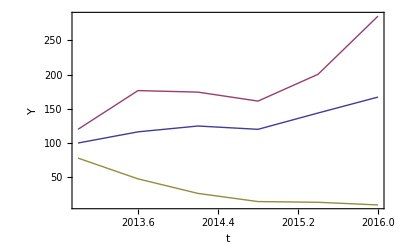

```mathematica
WWW=MultiDimSDEsolver[b,c,y0,t0,t1,5];
Transpose[Transpose[WWW][[2]]]//TraditionalForm
Transpose[{Transpose[WWW][[1]],#}]&/@
Transpose[Transpose[WWW][[2]]]//TraditionalForm
ListPlot[Transpose[{Transpose[WWW][[1]],#}]&/@
Transpose[Transpose[WWW][[2]]],Frame->True,Joined->True,FrameLabel->{t,Y},PlotRange->{0,All}]
```

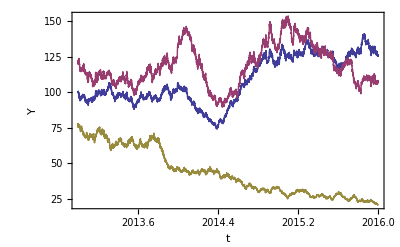

```mathematica
MultiTrajectory=MultiDimSDEsolver[{b,c,y0},{t0,t1,10000}];
ListPlot[Transpose[{Transpose[MultiTrajectory][[1]],#}]&/@Transpose[Transpose[MultiTrajectory][[2]]],Frame->True,Joined-> True,FrameLabel->{t,Y},PlotRange->{0,All}]
```